#### Temporal Memory Example - Sine and Sawtooth

#### Configuration

```mathematica
Get[  $UserBaseDirectory <> "/TriadicMemory/triadicmemoryC.m"]
Get[  $UserBaseDirectory <> "/TriadicMemory/temporalmemory.m"]
Get[  $UserBaseDirectory <> "/TriadicMemory/encoders.m"]
```

```mathematica
n = 1000; p = 5;
```

```mathematica
TemporalMemory[ T, {n,p}];
```

```mathematica
predict[x_] := SDR2Real[T[Real2SDR[x, {-1,1}, {n,p}]], {-1,1}, {n,p}]
```

#### 1. Learning a sine wave

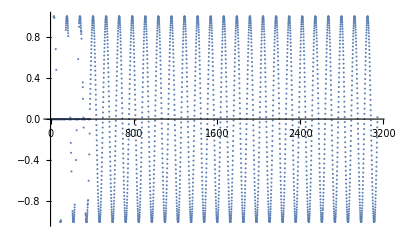

```mathematica
ListPlot[predict /@ Table[ Sin[x], {x,0,50Pi, 0.05}]]
```

#### 2. Learning a sawtooth wave

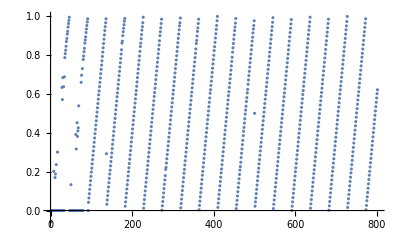

```mathematica
ListPlot[predict /@ Table[ SawtoothWave[0.22 x], {x,0,80, 0.1}]]
```

#### 3. Auto-playing

Starting from point -0.6, feeding each prediction back as input for the next step

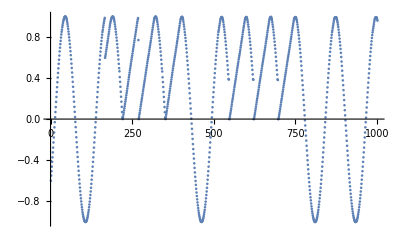

```mathematica
NestList[  predict, -0.6, 1000] // ListPlot
```